```mathematica
n=4;
```

```mathematica
coord={x,y,z,t};
```

```mathematica
metric=({{-1+ℊ[t,z]+O[ℊ[t,z]]^2, 𝒽[t,z]+O[𝒽[t,z]]^2, 0, 0}, {𝒽[t,z]+O[𝒽[t,z]]^2, -1-ℊ[t,z]+O[ℊ[t,z]]^2, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}});
```

```mathematica
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
christoffel:=christoffel=Simplify[Table[1/2 Sum[inversemetric[[i,s]](D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]];
```

```mathematica
listchristoffel=Table[If[UnsameQ[christoffel[[i,j,k]],0],{Style[ToString[Subscript[Γ, ToString[Mod[j,4]]<>ToString[Mod[k,4]]]^ToString[Mod[i,4]],StandardForm]<>"="<>ToString[christoffel[[i,j,k]],StandardForm]]}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],1],TableSpacing->{2,2}]
```

Γ_13^1=(-1/2 ℊ^(0,1)[t,z]-1/2 𝒽^(0,1)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_10^1=(-1/2 ℊ^(1,0)[t,z]-1/2 𝒽^(1,0)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_23^1=(-1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_20^1=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_31^1=(-1/2 ℊ^(0,1)[t,z]-1/2 𝒽^(0,1)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_32^1=(-1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_01^1=(-1/2 ℊ^(1,0)[t,z]-1/2 𝒽^(1,0)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_02^1=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_13^2=(-1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_10^2=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_23^2=(1/2 ℊ^(0,1)[t,z]-1/2 𝒽^(0,1)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_20^2=(1/2 ℊ^(1,0)[t,z]-1/2 𝒽^(1,0)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_31^2=(-1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_32^2=(1/2 ℊ^(0,1)[t,z]-1/2 𝒽^(0,1)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_01^2=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
Γ_02^2=(1/2 ℊ^(1,0)[t,z]-1/2 𝒽^(1,0)[t,z] 𝒽[t,z]+O[𝒽[t,z]]^2)+O[ℊ[t,z]]^1
Γ_11^3=(1/2 ℊ^(0,1)[t,z]+O[𝒽[t,z]]^3)+O[ℊ[t,z]]^1
Γ_12^3=(1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^2
Γ_21^3=(1/2 𝒽^(0,1)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^2
Γ_22^3=(-1/2 ℊ^(0,1)[t,z]+O[𝒽[t,z]]^3)+O[ℊ[t,z]]^1
Γ_11^0=(-1/2 ℊ^(1,0)[t,z]+O[𝒽[t,z]]^3)+O[ℊ[t,z]]^1
Γ_12^0=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^2
Γ_21^0=(-1/2 𝒽^(1,0)[t,z]+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^2
Γ_22^0=(1/2 ℊ^(1,0)[t,z]+O[𝒽[t,z]]^3)+O[ℊ[t,z]]^1

```mathematica
riemann:=riemann=Simplify[Table[D[christoffel[[i,j,l]],coord[[k]]]-D[christoffel[[i,j,k]],coord[[l]]]+Sum[christoffel[[s,j,l]]christoffel[[i,k,s]]-christoffel[[s,j,k]]christoffel[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{Style[ToString[Subscript[R, " "<>ToString[Mod[j,4]]<>ToString[Mod[k,4]]<>ToString[Mod[l,4]]]^ToString[Mod[i,4]],StandardForm]<>"="<>ToString[riemann[[i,j,k,l]],StandardForm]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}];
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],1],TableSpacing->{2,2}]
```

R_212^1=-M/r
R_221^1=M/r
R_313^1=-(M Sin[θ]^2)/r
R_331^1=(M Sin[θ]^2)/r
R_010^1=(2 M (2 M-r))/r^4
R_001^1=(2 M (-2 M+r))/r^4
R_112^2=-M/((2 M-r) r^2)
R_121^2=M/((2 M-r) r^2)
R_323^2=(2 M Sin[θ]^2)/r
R_332^2=-(2 M Sin[θ]^2)/r
R_020^2=(M (-2 M+r))/r^4
R_002^2=(M (2 M-r))/r^4
R_113^3=-M/((2 M-r) r^2)
R_131^3=M/((2 M-r) r^2)
R_223^3=-(2 M)/r
R_232^3=(2 M)/r
R_030^3=(M (-2 M+r))/r^4
R_003^3=(M (2 M-r))/r^4
R_110^0=(2 M)/((2 M-r) r^2)
R_101^0=-(2 M)/((2 M-r) r^2)
R_220^0=M/r
R_202^0=-M/r
R_330^0=(M Sin[θ]^2)/r
R_303^0=-(M Sin[θ]^2)/r

```mathematica
geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] u[Mod[j,4]] u[Mod[k,4]],{j,1,n},{k,1,n}],{i,1,n}]];
```

```mathematica
listgeodesic=Table[{Style[ToString[du^ToString[Mod[i,4]]/dτ,StandardForm]<>"="<>ToString[geodesic[[i]]/.{u[1]->(Superscript[u,1]),u[2]->(Superscript[u,2]),u[3]->(Superscript[u,3]),u[0]->(Superscript[u,0])},StandardForm]]},{i,1,n}];
```

```mathematica
TableForm[listgeodesic,TableSpacing->{2,2}]
```

du^1/dτ=((u u ℊ^(0,1)[t,z]+u u 𝒽^(0,1)[t,z]+u u ℊ^(1,0)[t,z]+u u 𝒽^(1,0)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
du^2/dτ=((-u u ℊ^(0,1)[t,z]+u u 𝒽^(0,1)[t,z]-u u ℊ^(1,0)[t,z]+u u 𝒽^(1,0)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
du^3/dτ=((1/2 (-(u)^2+(u)^2) ℊ^(0,1)[t,z]-u u 𝒽^(0,1)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
du^0/dτ=((1/2 ((u)^2-(u)^2) ℊ^(1,0)[t,z]+u u 𝒽^(1,0)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1

```mathematica
spingeodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] S[Mod[j,4]] u[Mod[k,4]],{j,1,n},{k,1,n}],{i,1,n}]];
```

```mathematica
listspingeodesic=Table[{Style[ToString[dS^ToString[Mod[i,4]]/dτ,StandardForm]<>"="<>ToString[spingeodesic[[i]]/.{u[1]->(Superscript[u,1]),u[2]->(Superscript[u,2]),u[3]->(Superscript[u,3]),u[0]->(Superscript[u,0]),S[1]->(Superscript[S,1]),S[2]->(Superscript[S,2]),S[3]->(Superscript[S,3]),S[0]->(Superscript[S,0])},StandardForm]]},{i,1,n}];
```

```mathematica
TableForm[listspingeodesic,TableSpacing->{2,2}]
```

dS^1/dτ=…
dS^2/dτ=…
dS^3/dτ=(1/2 ((S u-S u) ℊ^(0,1)[t,z]+(S u+S u) 𝒽^(0,1)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1
dS^0/dτ=(1/2 ((-S u+S u) ℊ^(1,0)[t,z]-(S u+S u) 𝒽^(1,0)[t,z])+O[𝒽[t,z]]^1)+O[ℊ[t,z]]^1

```mathematica
Solve[Simplify[geodesic[[1]],Assumptions->{u[2]==0,u[3]==0}]==0,u[1]]
```

{{u[1]→(r u[4]-𝓇 u[4])/r},{u[1]→(-r u[4]+𝓇 u[4])/r}}

```mathematica
xsoln=ConstantArray[0,36];
ysoln=ConstantArray[0,36];
For[i=-5,i<31,i++,{n[t_]=(√(x[t]^2+y[t]^2))/(-10+√(x[t]^2+y[t]^2)),nx[t_]=-(x[t] 10)/(√(x[t]^2+y[t]^2) (√(x[t]^2+y[t]^2)-10)^2),ny[t_]=-(y[t] 10)/(√(x[t]^2+y[t]^2) (√(x[t]^2+y[t]^2)-10)^2),sol=NDSolve[{x'[t]==vx[t]/n[t],y'[t]==vy[t]/n[t],vx'[t]==nx[t],vy'[t]==ny[t],x[0]==-100,y[0]==-2.245+4 i,vx[0]==n[0],vy[0]==0},{x[t],y[t],vx[t],vy[t]},{t,0,2000}],xsoln[[i+6]]=sol[[1,1]],ysoln[[i+6]]=sol[[1,2]]}]
```

NDSolve::ndsz: At t == 101.595, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 97.3511, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 94.298, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
color={RGBColor[0.27,0.45,0.6],RGBColor[0.95,0.58,0.29],RGBColor[0.44,0.69,0.38],RGBColor[0.8,0.36,0.35],RGBColor[0.61,0.49,0.75],RGBColor[0.6,0.46,0.42],RGBColor[0.86,0.59,0.79],RGBColor[0.57,0.57,0.57],RGBColor[0.78,0.78,0.38],RGBColor[0.42,0.78,0.84]};
plots=ConstantArray[0,36];
For[i=1,i<37,i++,plots[[i]]=ParametricPlot[{x[t]/.xsoln[[i]],y[t]/.ysoln[[i]]},{t,0,2000},PlotRange->{{-100,100},{-100,100}},Frame->True,Axes->False,PlotStyle->color[[Mod[i,10,1]]]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

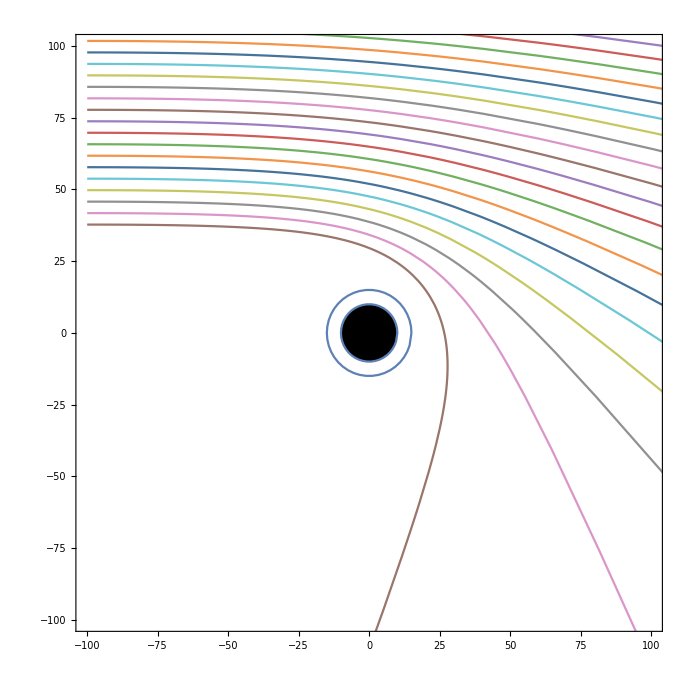

```mathematica
schwarzschild=RegionPlot[Disk[{0,0},10],PlotStyle->Black];
sphere=RegionPlot[Circle[{0,0},15],PlotStyle->Black];
Show[plots,schwarzschild, sphere]
```